```mathematica
spherePoint[dim_]:=Table[RandomVariate[NormalDistribution[]],dim]//Normalize;
```

```mathematica
feasibilifySimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords,multipliers},
lastVertexNewCoords=-Last[vertices].Inverse[m];
multipliers=Append[If[#>=0,1,-1]&/@lastVertexNewCoords,If[Total[lastVertexNewCoords]<=1,1,-1]];
vertices*multipliers
];
```

```mathematica
generateSimplexWithZeroInside[dim_]:=feasibilifySimplex[Table[spherePoint[dim],dim+1]];
```

```mathematica
simplexVolume[vertices_]:=Abs@Det[(#-First[vertices])&/@Rest[vertices]]/(Length[vertices]-1);
```

```mathematica
averageVolumes=Table[Mean[simplexVolume/@Table[generateSimplexWithZeroInside[n],1000]],{n,2,30}]
```

{0.950406,0.517402,0.306644,0.178541,0.107652,0.0634167,0.037195,0.0216098,0.0140878,0.00826413,0.00489048,0.00280481,0.00175761,0.000981027,0.000661598,0.000410429,0.000245614,0.000143891,0.0000852435,0.0000511834,0.0000312117,0.0000201014,0.0000115472,7.21414×10^-6,4.48432×10^-6,2.54573×10^-6,1.47032×10^-6,9.28817×10^-7,6.10776×10^-7}

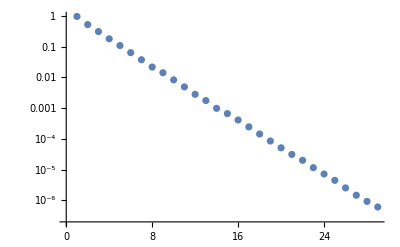

```mathematica
ListLogPlot[averageVolumes]
```